# НЕЛИНЕЙНАЯ ФИЗИКА

## Pr1

Найти все существующие особые (неподвижные) точки заданной динамической
системы

```mathematica
f[x_,y_]=y;
g[x_,y_]=(a+b*y^2-y^4) *y-x;
```

```mathematica
Solve[f[x,y]==0&&g[x,y]==0,{x,y}]
```

{{x→0,y→0}}

## Pr2

Фазовый портрет

```mathematica
Manipulate[StreamPlot[{y,(a+b*y^2-y^4) *y-x},{x,-0.5,0.5},{y,-0.5,0.5}],{a,-5,5},{b,-5,5}]
```

## Pr3

Линейный анализ устойчивости особых точек

```mathematica
y0=0;
x0=0;
flin[q_,p_]=D[f[x,y],x]*q+D[f[x,y],y]*p/.{x->x0,y->y0}
glin[q_,p_]=D[g[x,y],x]*q+D[g[x,y],y]*p/.{x->x0,y->y0}
```

p

a p-q

#### след матрицы Якоби и её детерминант

```mathematica
s=D[f[x,y],x]+D[g[x,y],y]/.{x->x0,y->y0}
j=D[f[x,y],x]*D[g[x,y],y]-D[f[x,y],y]*D[g[x,y],x]/.{x->x0,y->y0}
```

a

1

#### решение характеристического уравнения

```mathematica
λ1[a_,b_]=s/2+Sqrt[s^2/4-j]
λ2[a_,b_]=s/2-Sqrt[s^2/4-j]
```

a/2+√(-1+a^2/4)

a/2-√(-1+a^2/4)

#### Анализ устойчивости

```mathematica
Reduce[Exists[{λ1,λ2},Re[λ1[a,b]]<0&&Re[λ2[a,b]]<0],{a,b}]
```

Re[a]<0

#### Типы особых точек

уст. узел

```mathematica
Reduce[Exists[{λ1,λ2},Re[λ1[a,b]]<0&&Re[λ2[a,b]]<0&&Im[λ2[a,b]]==0],{a,b}]
```

Re[a]≤-2&&Im[a]==0

неуст. узел

```mathematica
Reduce[Exists[{λ1,λ2},Re[λ1[a,b]]>0&&Re[λ2[a,b]]>0&&Im[λ2[a,b]]==0],{a,b}]
```

Re[a]≥2&&Im[a]==0

уст. фокус

```mathematica
Reduce[Exists[{λ1,λ2},Re[λ1[a,b]]<0&&Re[λ2[a,b]]<0&&Im[λ2[a,b]]≠0],{a,b}]
```

(Im[a]≠0&&Re[a]≤-2)||-2<Re[a]<0

неуст. фокус

```mathematica
Reduce[Exists[{λ1,λ2},Re[λ1[a,b]]>0&&Re[λ2[a,b]]>0&&Im[λ2[a,b]]≠0],{a,b}]
```

0<Re[a]<2||(Im[a]≠0&&Re[a]≥2)

седло

```mathematica
Reduce[Exists[{λ1,λ2},Im[λ2[a,b]]==0&&Re[λ1[a,b]]*Re[λ2[a,b]]<0],{a,b}]
```

False

центр

```mathematica
Reduce[Exists[{λ1,λ2},Re[λ1[a,b]]==0&&Re[λ2[a,b]]==0&&Im[λ2[a,b]]≠0],{a,b}]
```

Re[a]==0

#### бифуркационные диаграммы

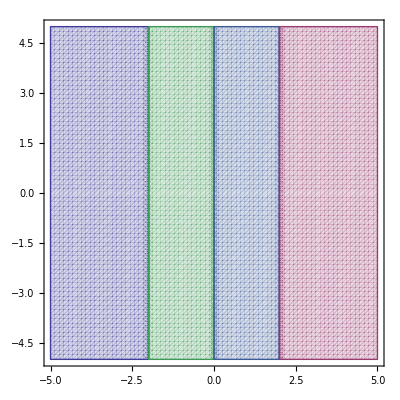

```mathematica
RegionPlot[{Re[λ1[a,b]]<0&&Re[λ2[a,b]]<0&&Im[λ2[a,b]]==0,
Re[λ1[a,b]]>0&&Re[λ2[a,b]]>0&&Im[λ2[a,b]]==0,
Re[λ1[a,b]]==0&&Re[λ2[a,b]]==0&&Im[λ2[a,b]]≠0,
Re[λ1[a,b]]<0&&Re[λ2[a,b]]<0&&Im[λ2[a,b]]≠0,
Re[λ1[a,b]]>0&&Re[λ2[a,b]]>0&&Im[λ2[a,b]]≠0},{a,-5,5},{b,5,-5},PlotPoints -> 75]
```

## Pr4

Коши

#### уст. узел справа (a+b*y^2-y^4) *y-x

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

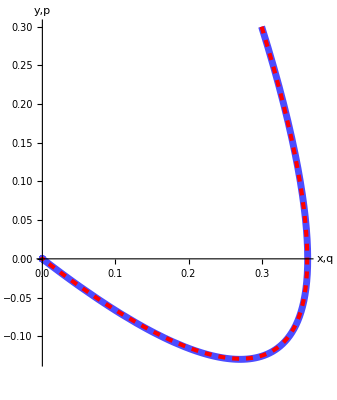

```mathematica
sol1=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==y[0]==0.3},{x,y},{t,0,100}]/.{a->-2.1,b->1};
sol2=DSolve[{q'[t]==p[t],p'[t]==a*p[t]-q[t],q[0]==p[0]==0.3},{p,q},t]/.{a->-2.1,b->1};
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol1],Evaluate[{q[t],p[t]}/.sol2]},{t,0,100}, PlotRange->All,PlotStyle->{{Directive[Blue,AbsoluteThickness[5],Opacity[0.7]]},Directive[Red,AbsoluteThickness[3],Dashed]},AxesLabel->{"x,q","y,p"}]
```

#### неуст. фокус внутри пред. цикла

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

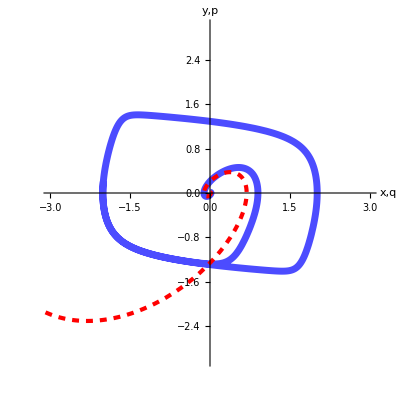

```mathematica
sol1=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==y[0]==0.01},{x,y},{t,0,20}]/.{a->1,b->1};
sol2=DSolve[{q'[t]==p[t],p'[t]==a*p[t]-q[t],q[0]==p[0]==0.01},{p,q},t]/.{a->1,b->1};
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol1],Evaluate[{q[t],p[t]}/.sol2]},{t,0,20}, PlotRange->{-3,3},PlotStyle->{{Directive[Blue,AbsoluteThickness[5],Opacity[0.7]]},Directive[Red,AbsoluteThickness[3],Dashed]},AxesLabel->{"x,q","y,p"}]
```

#### неуст. фокус снаружи пред. цикла

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

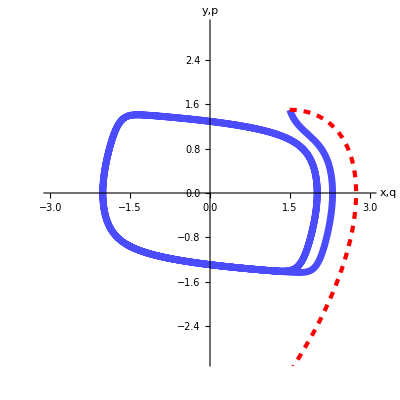

```mathematica
sol1=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==y[0]==1.5},{x,y},{t,0,20}]/.{a->1,b->1};
sol2=DSolve[{q'[t]==p[t],p'[t]==a*p[t]-q[t],q[0]==p[0]==1.5},{p,q},t]/.{a->1,b->1};
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol1],Evaluate[{q[t],p[t]}/.sol2]},{t,0,20}, PlotRange->{-3,3},PlotStyle->{{Directive[Blue,AbsoluteThickness[5],Opacity[0.7]]},Directive[Red,AbsoluteThickness[3],Dashed]},AxesLabel->{"x,q","y,p"}]
```

## Pr5

Пуанкаре

```mathematica
Manipulate[VectorPlot[(#/Norm[#])&@{y,(a+b*y^2-y^4) *y-x}/.{a->#},{x,-1,1},{y,-1,1},StreamPoints->15,StreamStyle->{Purple, AbsoluteThickness[1.8]}]&/@{-3,-2,-1,0,1,2},{b,-5,5}]
```

Вертикальная изоклина для х (у)

```mathematica
Solve[(a+b*y^2-y^4) *y==0]
```

{{a→-b y^2+y^4},{y→0}}

```mathematica
Manipulate[Plot[(a+b*y^2-y^4) *y,{y,-2,2},AxesLabel->{"y","x"}],{a,-4,4},{b,-5,5}]
```

Фазовые траектории при устойчивом предельном цикле

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

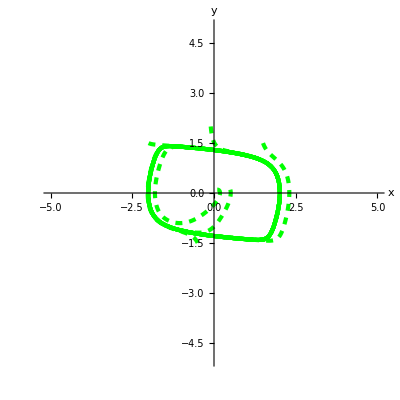

```mathematica
track1=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==y[0]==1.5},{x,y},{t,0,20}]/.{a->1,b->1};
track2=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==y[0]==0.1},{x,y},{t,0,20}]/.{a->1,b->1};
track3=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==0.5,y[0]==0.1},{x,y},{t,0,20}]/.{a->1,b->1};
track4=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],y[0]==1.5,x[0]==-2},{x,y},{t,0,20}]/.{a->1,b->1};track5=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],y[0]==-1.5,x[0]==-0.5},{x,y},{t,0,20}]/.{a->1,b->1};
track6=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],y[0]==2,x[0]==-0.1},{x,y},{t,0,20}]/.{a->1,b->1};
ParametricPlot[{Evaluate[{x[t],y[t]}/.track1],Evaluate[{x[t],y[t]}/.track2],Evaluate[{x[t],y[t]}/.track3],Evaluate[{x[t],y[t]}/.track4],Evaluate[{x[t],y[t]}/.track5],Evaluate[{x[t],y[t]}/.track6]},{t,0,20}, PlotRange->{-5,5},PlotStyle->{Directive[Green,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"}]
```

Фазовые траектории при неустойчивом предельном цикле

NDSolve::bdmtd: The value of the option Method -> {"TimeIntegration" → "ExplicitEuler"} is not a known built-in method, a symbol that could be a user-defined method, or a list with a name followed by method options.

General::stop: Further output of NDSolve :: bdmtd will be suppressed during this calculation.

NDSolve::bdmtd: The value of the option Method -> {"TimeIntegration" → "ExplicitEuler"} is not a known built-in method, a symbol that could be a user-defined method, or a list with a name followed by method options.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::bdmtd: The value of the option Method -> {"TimeIntegration" → "ExplicitEuler"} is not a known built-in method, a symbol that could be a user-defined method, or a list with a name followed by method options.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::bdmtd: The value of the option Method -> {"TimeIntegration" → "ExplicitEuler"} is not a known built-in method, a symbol that could be a user-defined method, or a list with a name followed by method options.

General::stop: Further output of NDSolve :: bdmtd will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

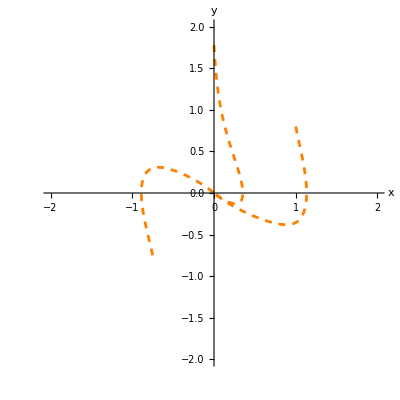

```mathematica
track1=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==-0.75,y[0]==-0.75},{x,y},{t,0,20}]/.{a->-2,b->-2};
track2=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==0,y[0]==1.77777777777777},{x,y},{t,0,20}]/.{a->-2,b->-2};
track3=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==1,y[0]==0.8},{x,y},{t,0,20}]/.{a->-2,b->-2};
track4=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],y[0]==1.1,x[0]==0.1},{x,y},{t,0,0.55},Method->{"TimeIntegration"->"ExplicitEuler"}]/.{a->-2,b->-2};
track5=

NDSolve[{x'[t]==y[t],y'[t]==(-2+2*y[t]^2-y[t]^4) *y[t]-x[t],y[0]==0,x[0]==1.6},{x,y},{t,0,1.69},Method->{"TimeIntegration"->"ExplicitEuler"}];track6=NDSolve[{x'[t]==y[t],y'[t]==−(-2+2*y[t]^2-y[t]^4) *y[t]-x[t],y[0]==-1.2,x[0]==-1.1},{x,y},{t,0,2.2},Method->{"TimeIntegration"->"ExplicitEuler"}];track7=NDSolve[{x'[t]==y[t],y'[t]==(-2+2*y[t]^2-y[t]^4) *y[t]-x[t],y[0]==-1.1,x[0]==0},{x,y},{t,0,0.49},Method->{"TimeIntegration"->"ExplicitEuler"}];
Show[ParametricPlot[{Evaluate[{x[t],y[t]}/.track1],Evaluate[{x[t],y[t]}/.track2],Evaluate[{x[t],y[t]}/.track3]},{t,0,20},PlotStyle->{Directive[Orange,AbsoluteThickness[2],Dashed]},AxesLabel->{"x","y"},PlotRange->{-2,2}],ParametricPlot[{Evaluate[{x[t],y[t]}/.track4]},{t,0,0.55},PlotStyle->{Directive[Orange,AbsoluteThickness[2],Dashed]}],ParametricPlot[{Evaluate[{x[t],y[t]}/.track5]},{t,0,1.69},PlotStyle->{Directive[Orange,AbsoluteThickness[2],Dashed]}],ParametricPlot[{Evaluate[{x[t],y[t]}/.track6]},{t,0,2.2},PlotStyle->{Directive[Orange,AbsoluteThickness[2],Dashed]}],ParametricPlot[{Evaluate[{x[t],y[t]}/.track7]},{t,0,0.49},PlotStyle->{Directive[Orange,AbsoluteThickness[2],Dashed]}]]
```

Построение сечения Пуанкаре

```mathematica
diffur=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==0.1,y[0]==0.11},{x,y},{t,0,100}]/.{a->1,b->1};
k=0;
data=Block[{a=1,b=1},Reap[NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],y[0]==0.1,x[0]==0.11,WhenEvent[{x[t]==0 &&x'[t]>0},{Sow[{x[t],y[t]}],k++,time[k]=t}]},{},{t,0,200},MaxSteps->∞]]][[-1,1]];
Show[ListPlot[data,ImageSize->Large,PlotRange->{{-3,3},All},PlotStyle->{Directive[Green,PointSize[0.010]]}],ParametricPlot[{Evaluate[{x[t],y[t]}/.diffur]},{t,0,200}, PlotRange->{-1.5,1.5},PlotStyle->{Directive[Orange,AbsoluteThickness[2],Dashed]},AxesLabel->{"x","y"}],PlotRange->{{-1.3,1.3},{-1.3,1.3}}]
qw=Table[{time[i],data[[i,2]]},{i,1,k}];
For[i=5,i≤25,i++,Tcycle[i]=time[i+1]-time[i]]
Tcycle[10]
ListPlot[qw,AxesLabel->{"t","y"},PlotRange->All,PlotStyle->{Directive[Green,PointSize[0.020]]}]
```

## Pr5.5

Алгоритм Эно

∂_t x=y
∂_t y=(a+b*y^2-y^4) *y-x
секущая поверхность S(x,y): x=0

```mathematica
a=1;b=1;
ur1[x_,y_]=y;
ur2[x_,y_]=(a+b*y^2-y^4) *y-x;
S[x_]=x;
H[x_,y_]=D[S[x],x]*ur1[x,y]
```

y

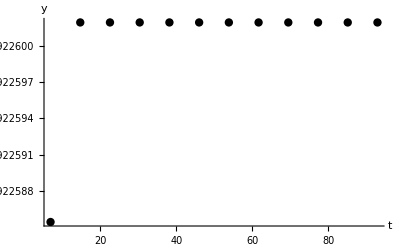

```mathematica
n=100000;
dt=0.001;
timeX={};
x0=0.1;
y0=0.1;
For[i=1,i≤n,i++,
xi=x0+ur1[x0,y0]*dt;
yi=y0+ur2[x0,y0]*dt;
If[(S[xi]*S[x0]<0 &&(xi-x0)>0),

timeX=Append[timeX,{dt*(i-1)-S[x0]/H[x0,y0],y0-(S[x0]ur2[x0,y0])/H[x0,y0]}];];
y0=yi;
x0=xi;
Clear[xi,yi]]
ListPlot[timeX,PlotRange->All,AxesLabel->{"t","y"},PlotStyle->{Directive[Black,PointSize[0.015]]}]
```

## Pr6

Расчет для устойчивого цикла

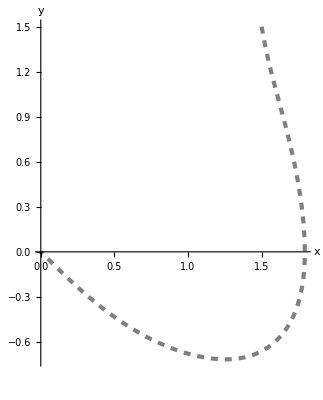

{{0.000478742,-0.000467115}}

```mathematica
resh1=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==y[0]==1.5},{x,y},{t,0,10}]/.{a->-2,b->1};
ParametricPlot[Evaluate[{x[t],y[t]}/.resh1],{t,0,11}, PlotRange->All,PlotStyle->{Directive[Gray,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"}]
tchk0=Evaluate[{x[10],y[10]}/.resh1]
a=-2;
b=1;
func1[x_,y_]=y;
func2[x_,y_]=(a+b*y^2-y^4) *y-x;
```

```mathematica
x0=tchk0[[1,1]];
y0=tchk0[[1,2]];
T=0.001;
eps= 0.001;
n=10000;
xi=0.003;
yi=0.004;
For[i=1,i≤n,i++,
reshi[i]=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==x0,y[0]==y0},{x,y},{t,0,T}]/.{a->-2,b->1};
reshj[i]=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==x0+xi,y[0]==y0+yi},{x,y},{t,0,T}]/.{a->-2,b->1};
tchki0=Evaluate[{x[T],y[T]}/.reshi[i]];
tchki1=Evaluate[{x[T],y[T]}/.reshj[i]];
x0=tchki0[[1,1]];
y0=tchki0[[1,2]];
vec=tchki1-tchki0;
x1=vec[[1,1]];
y1=vec[[1,2]];
xi=x1/Sqrt[x1^2+y1^2]*eps;
yi=y1/Sqrt[x1^2+y1^2]*eps;
deriv[i]=Sqrt[x1^2+y1^2];]
Λ=1/n/T*Sum[Log[deriv[i]/eps],{i,1,n,1}]
```

-0.541084

Расчет для неустойчивого цикла

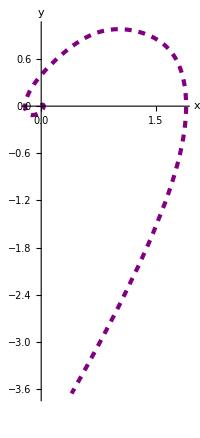

{{1.8963,-0.145373}}

```mathematica
resh2=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==0,y[0]==0.01},{x,y},{t,0,10}]/.{a->1,b->1};
ParametricPlot[Evaluate[{x[t],y[t]}/.resh2],{t,0,11}, PlotRange->All,PlotStyle->{Directive[Purple,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"}]
tchk20=Evaluate[{x[10],y[10]}/.resh2]
a=1;b=1;
func1[x_,y_]=y;
func2[x_,y_]=(a+b*y^2-y^4) *y-x;
```

```mathematica
x0=tchk20[[1,1]];
y0=tchk20[[1,2]];
T=0.001;
eps= 0.0005;
n=1000;
xi=0.0004;
yi=0.0003;
For[i=1,i≤n,i++,
reshi[i]=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==x0,y[0]==y0},{x,y},{t,0,T}]/.{a->1,b->1};
reshj[i]=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==x0+xi,y[0]==y0+yi},{x,y},{t,0,T}]/.{a->1,b->1};
tchki0=Evaluate[{x[T],y[T]}/.reshi[i]];
tchki1=Evaluate[{x[T],y[T]}/.reshj[i]];
x0=tchki0[[1,1]];
y0=tchki0[[1,2]];
vec=tchki1-tchki0;
x1=vec[[1,1]];
y1=vec[[1,2]];
xi=x1/Sqrt[x1^2+y1^2]*eps;
yi=y1/Sqrt[x1^2+y1^2]*eps;
deriv[i]=Sqrt[x1^2+y1^2];]
Λ=1/n/T*Sum[Log[deriv[i]/eps],{i,1,n,1}]
```

0.0282222

## Pr6.5

ЖОПЭЭЭЭ

```mathematica
resh0=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==y[0]==1.5},{x,y},{t,0,20}]/.{a->1,b->1};
tchk0=Evaluate[{x[20],y[20]}/.resh0]
a=1;b=1;
func1[x_,y_]=y;
func2[x_,y_]=(a+b*y^2-y^4) *y-x;
```

{{0.0005,-0.050223}}

{{0.0005,-0.050223},{0.001,-0.0301067}}

{{0.0005,-0.050223},{0.001,-0.0301067},{0.0015,-0.00210464}}

{{0.0005,-0.050223},{0.001,-0.0301067},{0.0015,-0.00210464},{0.002,-0.0165212}}

{{0.0005,-0.050223},{0.001,-0.0301067},{0.0015,-0.00210464},{0.002,-0.0165212},{0.0025,-0.00171278}}

{{0.0005,-0.050223},{0.001,-0.0301067},{0.0015,-0.00210464},{0.002,-0.0165212},{0.0025,-0.00171278},{0.003,-0.0087041}}

{{0.0005,-0.050223},{0.001,-0.0301067},{0.0015,-0.00210464},{0.002,-0.0165212},{0.0025,-0.00171278},{0.003,-0.0087041},{0.0035,-0.00530415}}

{{0.0005,-0.050223},{0.001,-0.0301067},{0.0015,-0.00210464},{0.002,-0.0165212},{0.0025,-0.00171278},{0.003,-0.0087041},{0.0035,-0.00530415},{0.004,-0.0100716}}

{{0.0005,-0.050223},{0.001,-0.0301067},{0.0015,-0.00210464},{0.002,-0.0165212},{0.0025,-0.00171278},{0.003,-0.0087041},{0.0035,-0.00530415},{0.004,-0.0100716},{0.0045,-0.00519038}}

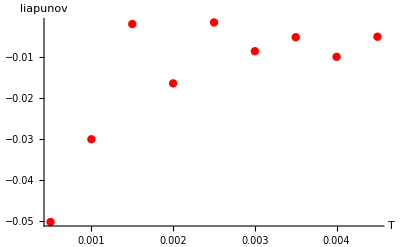

```mathematica
list={};
n=30000;
eps= 0.05;
tr=6;
Do[
x0=tchk0[[1,1]];
y0=tchk0[[1,2]];

For[d=0,d<tr,d++,
θ=π/3*d;
xi=eps Cos[θ];
yi=eps Sin[θ];
Clear[reshi,reshj,tchki0,tchki1,deriv];
For[i=1,i≤n,i++,
reshi[i]=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==x0,y[0]==y0},{x,y},{t,0,T}]/.{a->1,b->1};
reshj[i]=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==x0+xi,y[0]==y0+yi},{x,y},{t,0,T}]/.{a->1,b->1};
tchki0=Evaluate[{x[T],y[T]}/.reshi[i]];
tchki1=Evaluate[{x[T],y[T]}/.reshj[i]];
x0=tchki0[[1,1]];
y0=tchki0[[1,2]];
vec=tchki1-tchki0;
x1=vec[[1,1]];
y1=vec[[1,2]];
xi=x1/Sqrt[x1^2+y1^2]*eps;
yi=y1/Sqrt[x1^2+y1^2]*eps;
deriv[i]=Sqrt[x1^2+y1^2];];
liapunov1[d]=1/(n*T)*Sum[Log[deriv[i]/eps],{i,1,n,1}];];
liapunov=Sum[liapunov1[d],{d,0,tr-1,1}]/tr;
list=Append[list,{T,liapunov}];
Print[list];,{T,0.0005,0.0045,0.0005}]
ListPlot[list,PlotRange->All,AxesLabel->{"T","liapunov"},PlotStyle->{Directive[Red,PointSize[0.015]]}, Joined->False]
```

## Pr7

стробоскопическое отображение

```mathematica
n=100;
w= π/2;
A= 1;
a=1;
b=1;
T=(2π)/w;
data7=Block[{a=1,b=1},Reap[NDSolve[{x'[t]==y[t]+A*Cos[w*t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==0,y[0]==0,WhenEvent[Mod[t,T]==0,Sow[{x[t],y[t]}]]},{},{t,0,T*n},MaxSteps->∞]]][[-1,1]];
sol7=NDSolve[{x'[t]==y[t]+A*Cos[w*t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t],x[0]==0,y[0]==0},{x,y},{t,0,T*n}];
qu=ListPlot[data7,PlotRange->All,PlotStyle->{Directive[Green,AbsoluteThickness[1],PointSize[0.02]]},AxesLabel->{"x","y"}];
er=ParametricPlot[Evaluate[{x[t],y[t]}/.sol7],{t,0,T*n},PlotStyle->{Directive[Green,AbsoluteThickness[1],Dashed]},AxesLabel->{"x","y"}];
Show[qu,PlotRange->All]
```

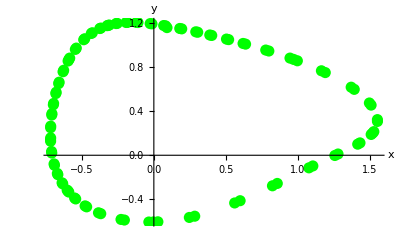

## Pr7.5

```mathematica
n=50;
A= 1;
a=1;
b=1;
Timecycle1=6.66328721;"!!!!!!!сечение пуанкаре"
data75=Block[{a=1,b=1},Reap[NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t]+A*Cos[w*t],x[0]==0.1,y[0]==0.11,WhenEvent[Mod[t,Timecycle1]==0,Sow[{x[t],y[t]}]]},{},{t,0,Timecycle1*n},MaxSteps->∞]]][[-1,1]];
resh75=NDSolve[{x'[t]==y[t],y'[t]==(a+b*y[t]^2-y[t]^4) *y[t]-x[t]+A*Cos[w*t],x[0]==0.1,y[0]==0.11},{x,y},{t,0,Timecycle1*n}];
qu=ListPlot[data75,PlotRange->All,PlotStyle->{Directive[PointSize[0.03],Purple]},AxesLabel->{"x","y"}];
er=ParametricPlot[Evaluate[{x[t],y[t]}/.resh75],{t,0,Timecycle1*n},PlotStyle->{Directive[Orange,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"}];
Show[qu,er,PlotRange->All]
time75=Table[{x[Timecycle1*i]/.resh75[[1]],y[Timecycle1*i]/.resh75[[1]]},{i,1,n}];
ListPlot[time75,AxesLabel->{"x","y"},PlotStyle->{Directive[Cyan,PointSize[0.01]]}]
```

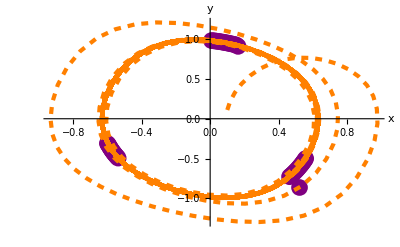

## Pr8

```mathematica
y'=a*(x^3/10-x)+b* y -b*y*x^2;
x'=y
":0417:0430:043c:0435:043d:0430"
x=ax
t'=bt
y=bx
"043 :0443:0440:0430:0432:043d:0435:043d:0438:044f"
y'=-x+y+1/a^2(x^3/10-y*x^2)
x'=ξy
```

```mathematica
Clear[a,b,x1,x2,y1,y2,ξ,x,y]
u1[x_,y_]=-x+y+κ(x^3/10-y*x^2);
u2[x_,y_]=ξ*y;
f1 = x0[t]+κ*x1[t]+κ^2*x2[t];
f2 = y0[t]+κ*y1[t]+κ^2*y2[t];
c1=CoefficientList[u1[f1,f2],κ];
c2=CoefficientList[u2[f1,f2],κ];
ξ=1/4;
sol0 = DSolve[{y0'[t]==c1[[1]],x0'[t]==c2[[1]],x0[0]==0,y0[0]==1},{x0[t],y0[t]},t]
x[t_]=x0[t]/.sol0[[1]];
y[t_]=y0[t]/.sol0[[1]];
sol1 = ( DSolve[{y1'[t]==(c1[[2]]/.x0[t]->x[t])/.y0[t]->y[t],x1'[t]==(c2[[2]]/.x0[t]->x[t])/.y0[t]->y[t],x1[0]==0,y1[0]==0},{x1[t],y1[t]},t])/.y0[t]->y[t]
```

```mathematica
Clear[x]
eqn:=x''[t]+x'[t]+ξ^2*x[t]-κ/ξ^2*(x[t]^3/10+ξ^2*x'[t]*x[t]^2);
x[t_]:=A1[t] ⅇ^(I ξ t)+A2[t] ⅇ^(-I ξ t);
cond=First[Solve[ⅇ^(I ξ t) A1'[t]+A2'[t] ⅇ^(-I ξ t)==0,A2'[t]]];
eq=Expand[(D[x'[t]/.cond,t]+x'[t]+ξ^2*x[t]-κ/ξ^2*(x[t]^3/10+ξ^2 x'[t]*x[t]^2))/ⅇ^(I ξ t)/.cond]
qconst = {A1[t]->A,A1'[t]->DA,A2[t]->CA};
e=Integrate[eq/.qconst,{t,0,2Pi/ξ}]
```

```mathematica
new={A->ρ[t]Exp[I*φ[t]],CA->ρ[t]Exp[-I*φ[t]],DA->D[ρ[t]Exp[I*φ[t]],t]};
eqf=e/.new;
s1=ComplexExpand[Re[eqf]];
s2=ComplexExpand[Im[eqf]];
sol=First[Solve[{s1==0,s2==0},{ρ'[t],φ'[t]}]]
```

```mathematica
sold=DSolve[{ρ'[t]==1/2 (-ρ[t]+κ ρ[t]^3),φ'[t]== -(3 κ ρ[t]^2)/(20 ξ^3)},{ρ[t],φ[t]},t]
```

```mathematica
x[t_]:=(ρ[t]*Exp[I*φ[t]]+ρ[t]*Exp[-I*φ[t]])/.sold[[1]]/.C[1]-> 0/.C[2]-> 0;
FullSimplify[x[t],Assumptions-> {ξ>0,t∈Reals,κ∈Reals}]
```

```mathematica
x[t_]=-(2 Cos[(3 (t-Log[ⅇ^t+κ]))/(20 ξ^3)])/(√(ⅇ^t+κ));
ξ=4;
κ=0.01;
soln=NDSolve[{x1''[t]+x1'[t]+ξ^2*x1[t]-κ/ξ^2*(x1[t]^3/10+ξ^2*x1'[t]*x1[t]^2)==0,x1[0]== x[0],x1'[0]==x'[0]},x1[t],{t,0,10}];
Plot[{Evaluate[x1[t]/.soln],x[t]*Re[Exp[I*ξ*t]]},{t,0,10}]
```